```mathematica
mcSim[β_,j_,n_,iter_]:=Module[{grid=Array[1&,{n,n}],x,y,r,diff,a,rejected=0},grids=Array[{}&,iter];
For[k=1,k≤iter,k++,
For[l=1,l≤n^2,l++,               (*sweep*)
x=RandomInteger[{1,n}];y=RandomInteger[{1,n}];diff=2*j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]);
a=If[diff>0,Exp[-β*diff],1];
r=RandomReal[];
If[a>r,grid[[x,y]]=-grid[[x,y]],rejected++];
];
grids[[k]]=grid
];
(*Print[rejected];*)
grids
]
magnetization[grids_,n_]:=1/(n^2*Dimensions[grids][[1]])*Total[Flatten[grids]]
magnetizationSq[grids_,n_]:=1/(Dimensions[grids][[1]])*Total[Flatten[Table[(1/n^2*Total[Flatten[grids[[i]]]])^2,{i,1,Dimensions[grids][[1]]}]]]
suscept[mag_,magSq_,β_]:=β*(magSq-mag^2)
energy[grids_,j_]:=Module[{grid,n},
sum=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
sum=sum+j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]);
];
];
];
sum/Dimensions[grids][[1]]
]
energySq[grids_,j_]:=Module[{grid,n,sum1},
sum=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
sum1=0;
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
sum1=sum1+(j*grid[[x,y]]*(grid[[Mod[x+1,n,1],y]]+grid[[Mod[x-1,n,1],y]]+grid[[x,Mod[y+1,n,1]]]+grid[[x,Mod[y-1,n,1]]]));
];
];
sum = sum + sum1^2;
];
sum/Dimensions[grids][[1]]
]
specificHeat[energy_,energySq_,β_]:=β^2*(energySq-energy^2)
magAntiferro[grids_]:=Module[{grid,n},
m=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
m=m+(-1)^(x+y)*grid[[x,y]]/n^2;
];
];
];
m/Dimensions[grids][[1]]
]
magAntiferroSq[grids_]:=Module[{grid,n,m1},
m=0;
n=Dimensions[grids[[1]]][[1]];
For[i=1,i≤Dimensions[grids][[1]],i++,
grid=grids[[i]];
m1=0;
For[x=1,x≤n,x++,
For[y=1,y≤n,y++,
m1=m1+(-1)^(x+y)*grid[[x,y]]/n^2;
];
];
m=m+m1^2;
];
m/Dimensions[grids][[1]]
]
```

```mathematica
n=20;j=1;steps=10000;
βs=Table[β,{β,0.0,0.7,0.01}];
s=AbsoluteTiming[Parallelize[Table[mcSim[βs[[i]],j,n,steps],{i,1,Dimensions[βs][[1]]}]]];
s[[1]]
simβvar=s[[2]];
simβvar=simβvar[[All,201;;-1]];
ms=Parallelize[Table[magnetization[simβvar[[i]],n],{i,1,Dimensions[simβvar][[1]]}]];
p1=Table[{βs[[i]],ms[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p1,PlotRange->All]
suscepts=Parallelize[Table[suscept[ms[[i]],magnetizationSq[simβvar[[i]],n],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}]];
p2=Table[{βs[[i]],suscepts[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p2,PlotRange->All]
heats=Parallelize[Table[specificHeat[energy[simβvar[[k]],j],energySq[simβvar[[k]],j],βs[[k]]],{k,1,Dimensions[βs][[1]]}]];
p3=Table[{βs[[i]],heats[[i]]},{i,1,Dimensions[βs][[1]]}];
ListLinePlot[p3,PlotRange->All]
(*ListLinePlot[Table[magAntiferro[simβvar[[i]]],{i,1,Dimensions[βs][[1]]}]]
(*susceptsAnti=Table[suscept[magAntiferro[simβvar[[i]]],magAntiferroSq[simβvar[[i]]],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}];*)
sAnti=Parallelize[Table[suscept[magAntiferro[simβvar[[t]]],magAntiferroSq[simβvar[[t]]],βs[[t]]],{t,1,Dimensions[βs][[1]]}]];
ListLinePlot[sAnti,PlotRange->All]*)
```

410.45771

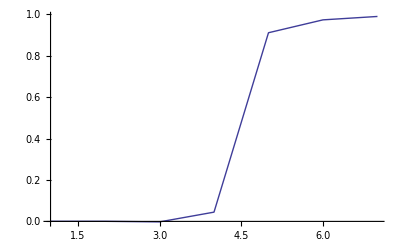

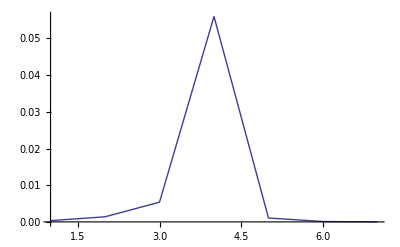

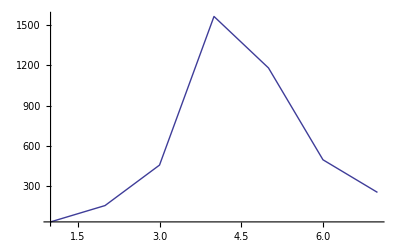

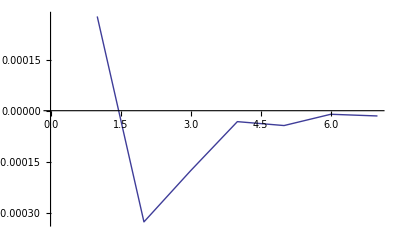

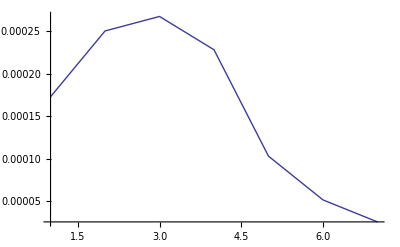

```mathematica
n=20;j=1;steps=50000;
βs=Table[β,{β,0.1,0.7,0.1}];
simβvar=Table[mcSim[βs[[i]],j,n,steps][[6;;-1]],{i,1,Dimensions[βs][[1]]}];
ms=Table[magnetization[simβvar[[i]],n],{i,1,Dimensions[simβvar][[1]]}];
ListLinePlot[ms,PlotRange->All]
suscepts=Table[suscept[ms[[i]],magnetizationSq[simβvar[[i]],n],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}];
ListLinePlot[suscepts,PlotRange->All]
heats=Table[specificHeat[energy[simβvar[[k]],j],energySq[simβvar[[k]],j],βs[[k]]],{k,1,Dimensions[βs][[1]]}];
ListLinePlot[heats,PlotRange->All]
ListLinePlot[Table[magAntiferro[simβvar[[i]]],{i,1,Dimensions[βs][[1]]}]]
(*susceptsAnti=Table[suscept[magAntiferro[simβvar[[i]]],magAntiferroSq[simβvar[[i]]],βs[[i]]],{i,1,Dimensions[simβvar][[1]]}];*)
sAnti=Table[suscept[magAntiferro[simβvar[[t]]],magAntiferroSq[simβvar[[t]]],βs[[t]]],{t,1,Dimensions[βs][[1]]}];
ListLinePlot[sAnti,PlotRange->All]
```

```mathematica
1/2.269//N
```

0.440723

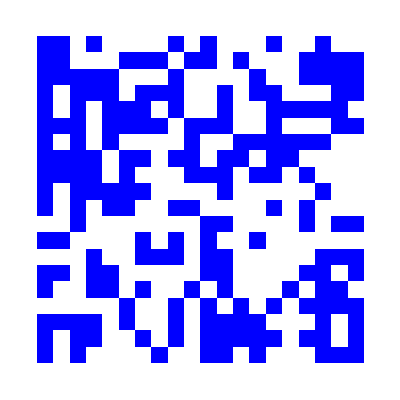
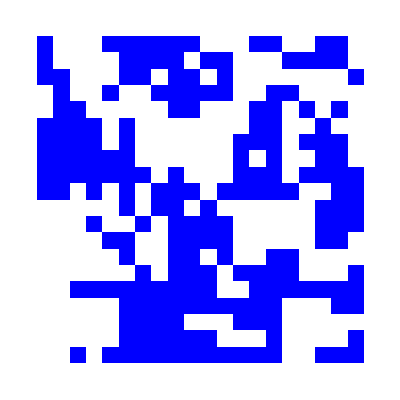
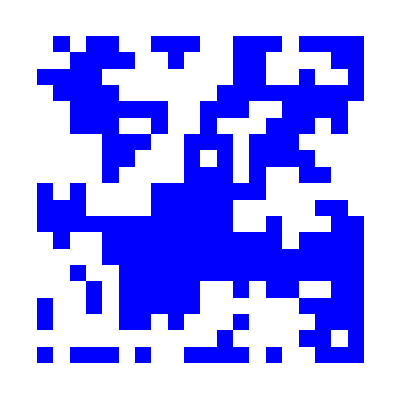
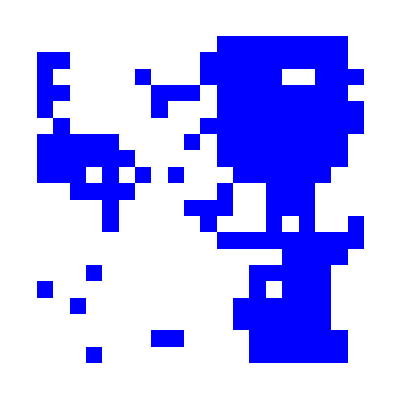
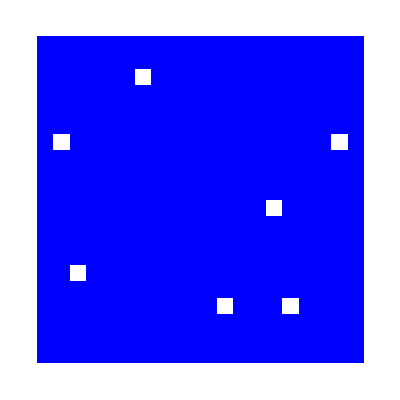
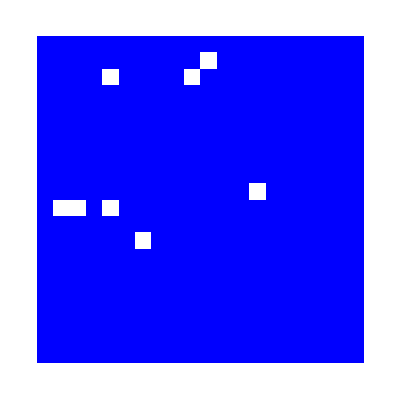
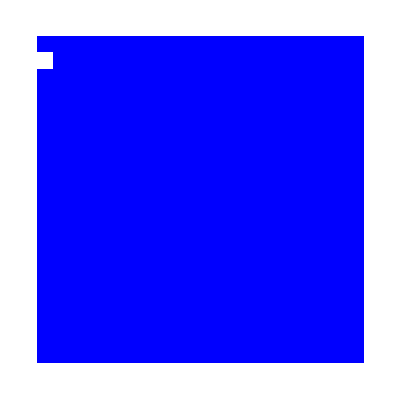

```mathematica
Table[ArrayPlot[simβvar[[i*1,90]],ColorRules->{1->Blue,-1->White}],{i,1,7}]
```

```mathematica
β=1;
j=1;
n=10;
iter=10000;
dauer=AbsoluteTiming[mcSim[β,j,n,iter]];
dauer[[1]]
```

17.65402

```mathematica
com=Compile[{β,j,n,iter},mcSim[β,j,n,iter]];           (*bringt fast nichts*)
dauer1=AbsoluteTiming[mcSim[β,j,n,iter]];
dauer1[[1]]
```

17.67202

```mathematica
ByteCount[dauer[[2]]]
```

29280080

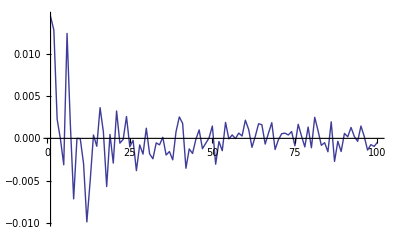

```mathematica
β=0;
j=1;
n=10;
maxiter=10000;
anzahl=100;
plt=Parallelize[Table[magnetization[mcSim[β,j,n,maxiter/anzahl*i],n],{i,1,anzahl}]];
ListLinePlot[plt,PlotRange->All]
```